## Lesson

Use natural language input to create units (ctrl =):

```mathematica
Quantity[10, "Hours"]
```

10 h

Convert between units:

```mathematica
UnitConvert[Quantity[10, "Hours"],"Minutes"]
```

600 min

Convert between currencies:

```mathematica
CurrencyConvert[Quantity["7.00", "BritishPounds"],"CzechKoruny"]
```

208.37 Kč

Rotate expression by angle:

```mathematica
Rotate["Australia",Quantity[180, "AngularDegrees"]]
```

Australia

Make a path using angles:

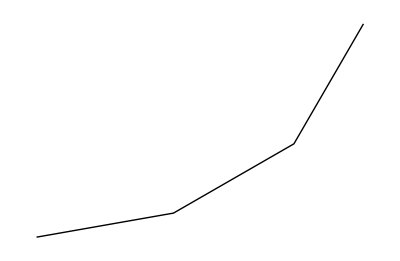

```mathematica
Graphics[Line[AnglePath[{Quantity[10, "AngularDegrees"],Quantity[20, "AngularDegrees"],Quantity[30, "AngularDegrees"]}]]]
```

## Questions

Q1. Convert 4.5 lbs (pounds) to kilograms.

```mathematica
UnitConvert[Quantity[4.5, "Pounds"],"Kilograms"]
```

2.04117 kg

Q2. Convert 60.25 mph to kilometers per hour.

```mathematica
UnitConvert[Quantity[60.25, ("Miles")/("Hours")],"KilometersPerHour"]
```

96.963 km/h

Q3. Find the height of the Eiffel Tower in miles.

```mathematica
UnitConvert[Entity["Building","EiffelTower::5h9w8"]["Height"],"Miles"]
```

0.205052 mi

Q4. Find the height of Mount Everest divided by the height of the Eiffel Tower.

```mathematica
(Entity["Mountain","MountEverest"]["Elevation"])/(Entity["Building","EiffelTower::5h9w8"]["Height"])
```

26.8147

Q5. Find the mass of the Earth divided by the mass of the Moon.

```mathematica
(Entity["Planet","Earth"]["Mass"])/(Entity["PlanetaryMoon","Moon"]["Mass"])
```

81.3

Q6. Convert 2500 Japanese yen to US dollars.

```mathematica
CurrencyConvert[Quantity[2500., "Yen"],"USDollars"]
```

17.31 $

Q7. Find the total of 35 ounces, 1/4 ton, 45 lbs and 9 stone in kilograms.

```mathematica
UnitConvert[Total[{Quantity[35, "Ounces"],Quantity[0.25, "ShortTons"],Quantity[45, "Pounds"],Quantity[9, "Stones"]}],"Kilograms"]
```

305.353 kg

Q8. Get a list of the distances to each planet using the “DistanceFromEarth” property, and convert all the results to light minutes.

```mathematica
UnitConvert[#["DistanceFromEarth"]&/@EntityList[EntityClass["Planet",All]],"LightMinutes"]
```

{6.25628 light minutes,12.7321 light minutes,0. light minutes,12.042 light minutes,42.9424 light minutes,72.1376 light minutes,161.264 light minutes,240.89 light minutes}

Q9. Rotate the string “hello” by 180°.

```mathematica
Rotate["hello",Quantity[180, "AngularDegrees"]]
```

hello

Q10. Make a table of a size-100 “A” rotated by 0° through 360° in steps of 30°.

```mathematica
Table[Rotate[Style["A",100],i °],{i,0,360,30}]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A}

Q11. Make a table of a size-100 “A” rotated by 0° through 360° in steps of 30°.

```mathematica
Manipulate[Rotate[Entity["TaxonomicSpecies","FelisCatus::ddvt3"]["Image"],i °],{i,0,180}]
```

Q12. Generate graphics for a path obtained by turning 0°, 1°, 2°, ... , 180°.

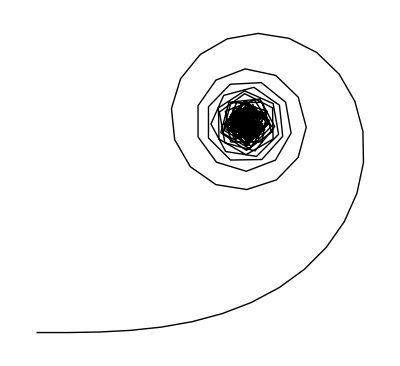

```mathematica
Graphics[Line[AnglePath[# °&/@Range[0,180]]]]
```

Q13. Make graphics of the path obtained by turning a constant angle 100 times, controlling the angle from 0° to 360° with a Manipulate.

```mathematica
Manipulate[Graphics[Line[AnglePath[Table[i °,100]]]],{i,0,360}]
```

Q14. Make graphics of the path obtained by successively turning by the digits of 2^10000 multiplied by 30°.

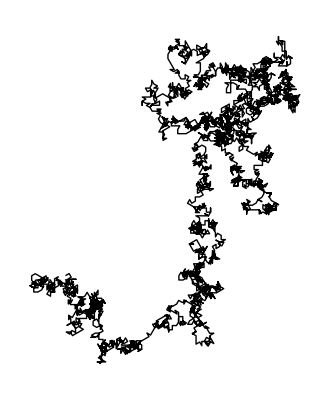

```mathematica
Graphics[Line[AnglePath[30° IntegerDigits[2^10000]]]]
```

## Extended Questions

+Q1. Convert 4.3 light years to furlongs.

```mathematica
UnitConvert[Quantity[4.3, "LightYears"],"Furlongs"]
```

2.02225×10^14 fur

+Q2. Convert 20,000 leagues to miles.

```mathematica
UnitConvert[Quantity[20000, "Leagues"],"Miles"]
```

60000 mi

+Q3. Make a Manipulate to rotate a size-200 “W” to any angle from 0° to 360°.

```mathematica
Manipulate[Rotate[Style["W",200],i °],{i,0,360}]
```

+Q4. Rotate an image of the Great Pyramid by 180°.

```mathematica
Rotate[Entity["Building","GreatPyramidOfGiza::jbm66"]["Image"],180°]
```

-Graphics-

+Q5. Generate a list of letters of the alphabet, each randomly rotated.

```mathematica
Rotate[#,RandomReal[360]°]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

+Q6. Generate graphics for a path obtained by turning 100 times through a random number of degrees between 0 and 360.

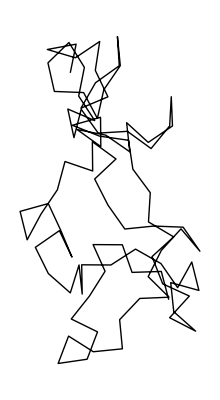

```mathematica
Graphics[Line[AnglePath[Table[RandomReal[360]°,100]]]]
```